REFERENCES

https : // www . scielosp . org/article/rpsp/1999. v5n1/1 - 8/

https : // www . researchgate . net/profile/Igor - Nesteruk/publication/343391770 _Waves _of _COVID - 19 _pandemic _Detection _and _SIR _simulations/links/5 f27d28a458515b729fe4be4/Waves - of - COVID - 19 - pandemic - Detection - and - SIR - simulations . pdf?origin = publication_detail

### Peak/Valleys Admission

```mathematica
(***FIRST: Indentigy the peaks and valleys of the epidemic curve until 17/08/2021*)
```

```mathematica
dataINS=Import["/home/lina/Documents/UnCover/datos_INS/2021-08-17.csv"];
```

```mathematica
dataINS[[1]]//PositionIndex
```

<|fecha_hoy_casos→{1},Caso→{2},Fecha Not→{3},Departamento→{4},Departamento_nom→{5},Ciudad_municipio→{6},Ciudad_municipio_nom→{7},Edad→{8},unidad_medida→{9},Sexo→{10},Fuente_tipo_contagio→{11},Ubicacion→{12},Estado→{13},Pais_viajo_1_cod→{14},Pais_viajo_1_nom→{15},Recuperado→{16},Fecha_inicio_sintomas→{17},Fecha_muerte→{18},Fecha_diagnostico→{19},Fecha_recuperado→{20},Tipo_recuperacion→{21},per_etn_→{22},nom_grupo_→{23}|>

```mathematica
cases=(DeleteCases[dataINS[[2;;,17]],""]//Tally)[[All,2]];
```

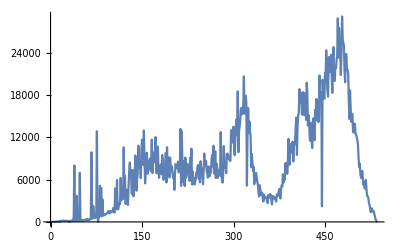

```mathematica
ListPlot[cases,Joined->True](**Aqui no está organizada por fechas*)
```

```mathematica
fechas[data_]:=Module[{fecha,template},
fecha=DateObject[ToExpression[Reverse[StringSplit[StringDrop[#,-8],"/"]]]]&/@DeleteCases[data,""];
template=Table["",data//Length];
MapThread[(template[[#1]]=#2)&,{Position[data/.""->Null,_?StringQ],fecha}];template]
```

```mathematica
dates=(DeleteCases[dataINS[[2;;,17]],""]//Tally)[[All,1]];
```

```mathematica
dates2=fechas[dates];
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/comparingDatesFormats.csv",Transpose[{dates,DateString/@dates2}]]
```

/home/lina/Documents/UnCover/datos_INS/comparingDatesFormats.csv

```mathematica
curve=Transpose[{dates2,cases}]//SortBy[#,First]&;
```

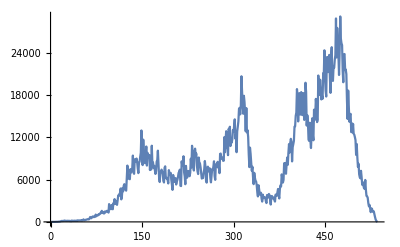

```mathematica
ListPlot[curve[[All,2]],Joined->True](**Aqui  está organizada por fechas*)
```

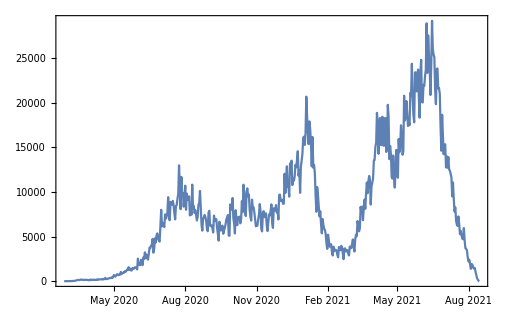

```mathematica
DateListPlot[Transpose[{dates2,cases}]](**Aqui  está organizada por fechas*)
```

```mathematica
(*********************so cases and dates2 are in desorder. Here I order them*)
```

```mathematica
date=(Transpose[{dates2,cases}]//SortBy[#,First]&)[[All,1]];
```

```mathematica
case=(Transpose[{dates2,cases}]//SortBy[#,First]&)[[All,2]];
```

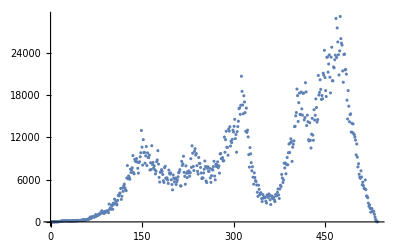

```mathematica
ListPlot[case]
```

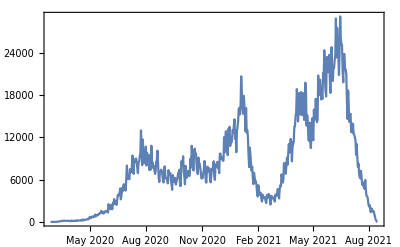

```mathematica
DateListPlot[Transpose[{date,case}]]
```

```mathematica
(*****************************************************************)
```

```mathematica
p=Transpose[{Sequence@@(NestList[RotateLeft[#]&,case,3][[2;;]]),case,Sequence@@(NestList[RotateRight[#]&,case,3][[2;;]])}];
```

```mathematica
smoothCases=Mean[#]&/@p;
```

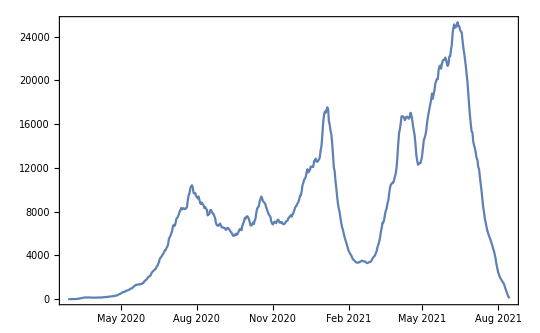

```mathematica
DateListPlot[Transpose[{date,smoothCases}]](**Aqui  está organizada por fechas*)
```

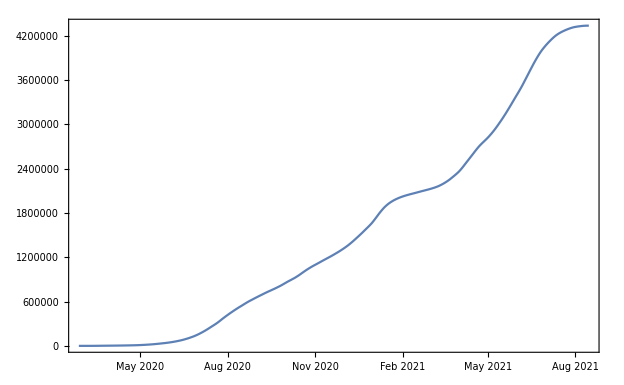

```mathematica
DateListPlot[Transpose[{date,Accumulate@smoothCases}]]
```

```mathematica
firstDerivate=(RotateLeft[smoothCases]-RotateRight[smoothCases])/2;
```

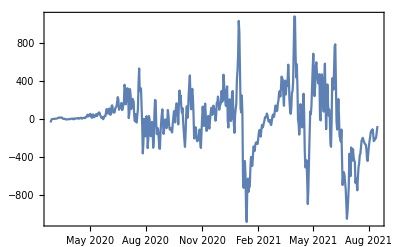

```mathematica
DateListPlot[Transpose[{date,firstDerivate}]]
```

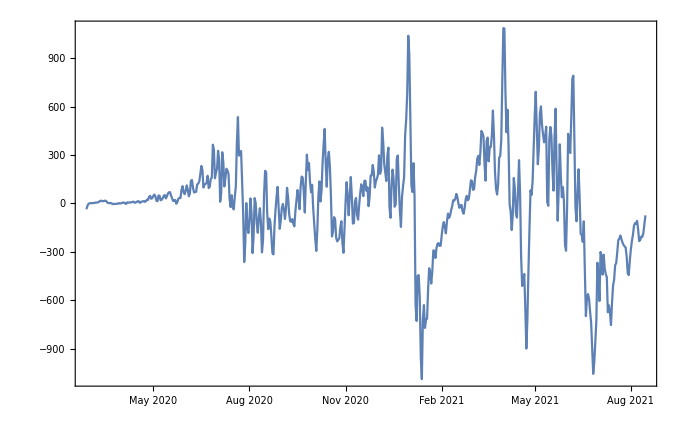

```mathematica
normalDerivada=firstDerivate/.{x_?Negative:>- x/Min[firstDerivate],x_?Positive:> x/Max[firstDerivate]};
```

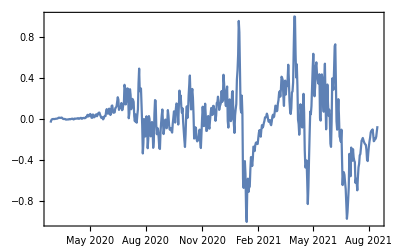

```mathematica
p1=DateListPlot[Transpose[{date,normalDerivada}]]
```

```mathematica
-Graphics-//InputForm
```

```mathematica
RGBColor
```

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black]]
```

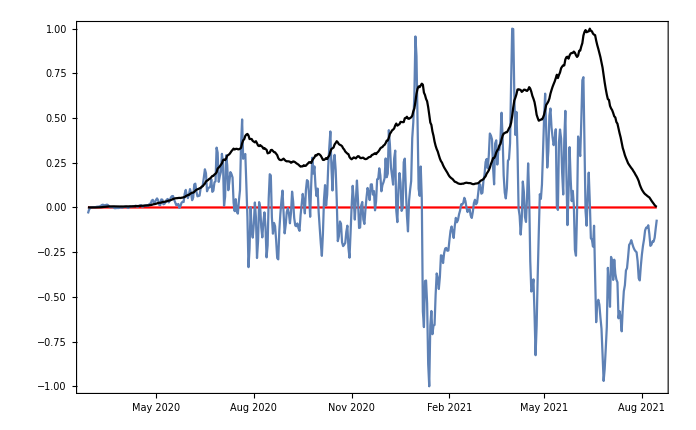
```mathematica
(-Graphics-_□)_□
```

```mathematica
(*NOTE: 2  options : 1. Make the ctaegories by cycles (derivative), 3. Make the categories by peaks and valleys*)
```

```mathematica
(******************************************************+)
```

```mathematica
segundaDerivate=(RotateLeft[smoothCases]-(2*smoothCases+RotateRight[smoothCases]));
```

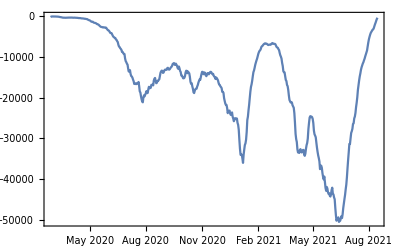

```mathematica
DateListPlot[Transpose[{date,segundaDerivate}]]
```

```mathematica
(***************************************************)
```

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black]]
```

-Graphics-

```mathematica
(**************************************Here we count the number of points under the thresholds -100/-100....- for x number of points -1,2,3,4 left/risht- around each point or day in firstDerivative*)
```

```mathematica
Table[Count[Round[#],Alternatives[Sequence@@Range[-100,100]]]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

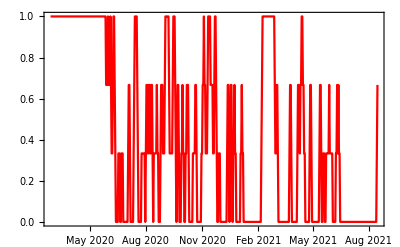
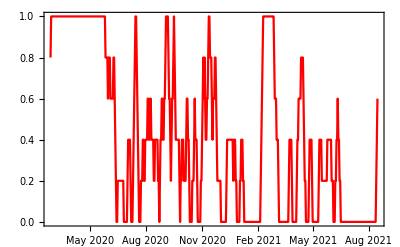
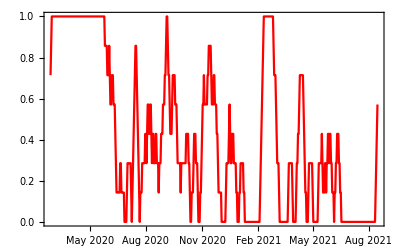
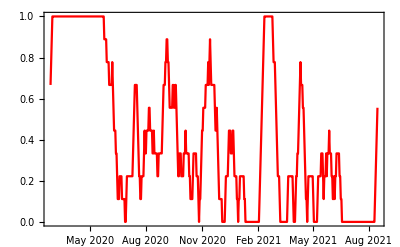

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

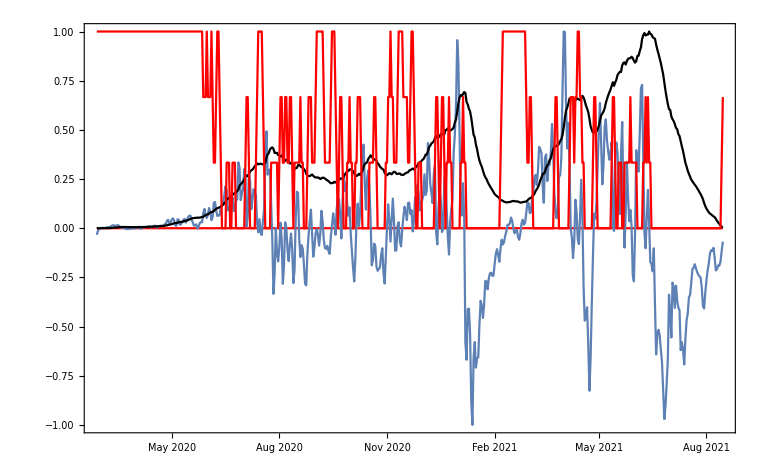

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%287[[1]]]
```

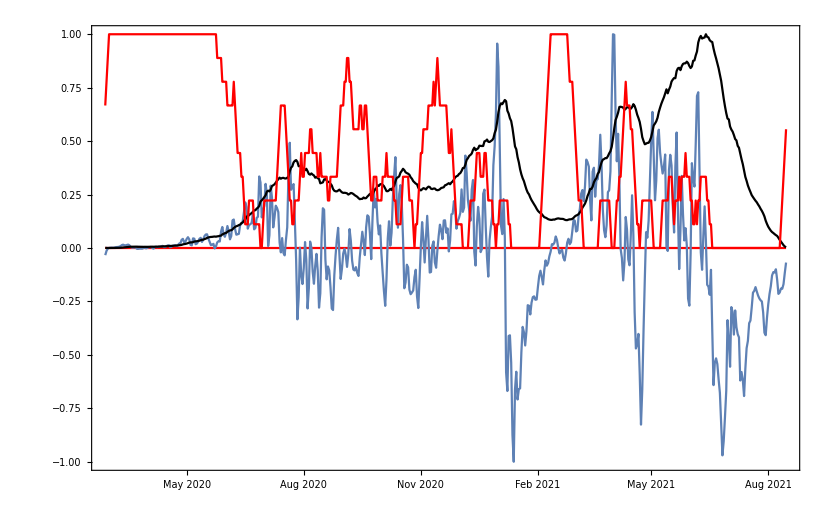

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%287[[-1]]](*Este es más claro que el anterior*)
```

```mathematica
mejor=Table[Count[Round[#],Alternatives[Sequence@@Range[-150,150]]]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

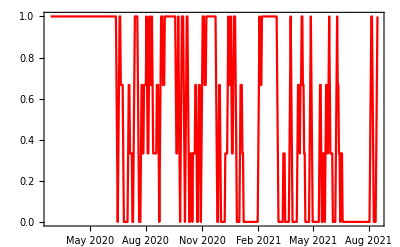
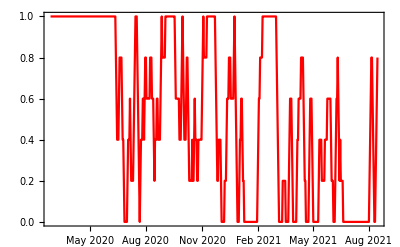
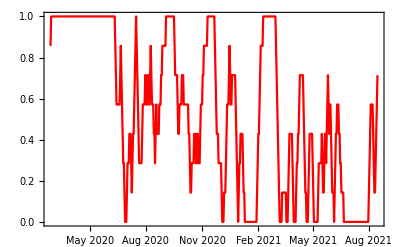
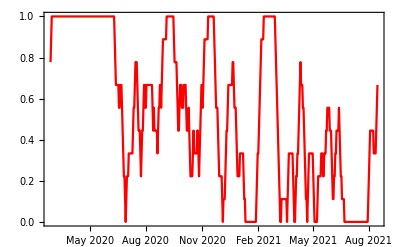

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

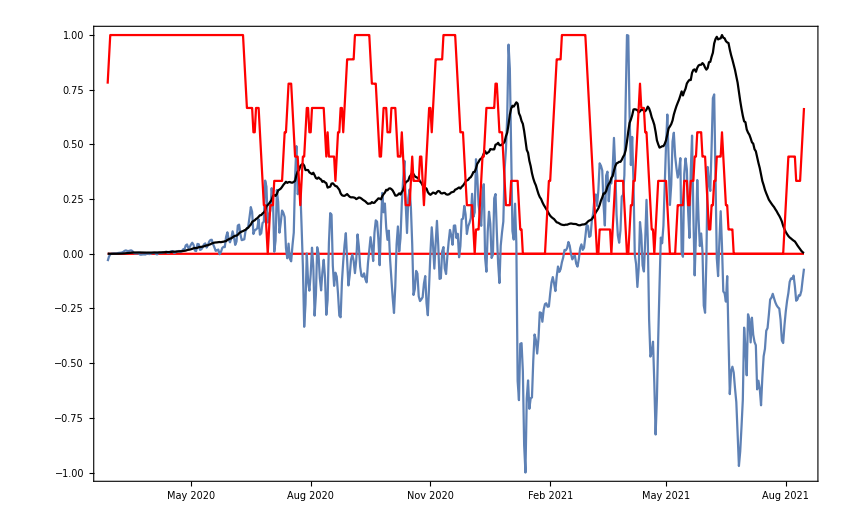

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%[[-1]]](*Es mejor indentificando los valles que los picos. Pero entre valle y valle hay un pico. Los siguiente sería identificar las fechas de los puntos más altos (rojo) y se parte la curva por esas fechas *)
```

```mathematica
Table[Count[Round[#],Alternatives[Sequence@@Range[-200,200]]]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

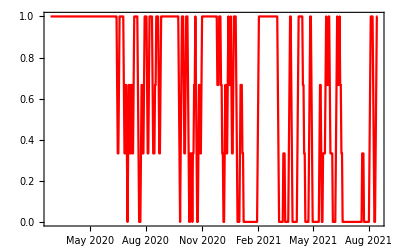
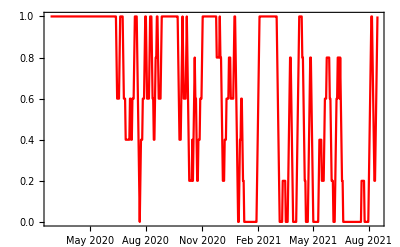
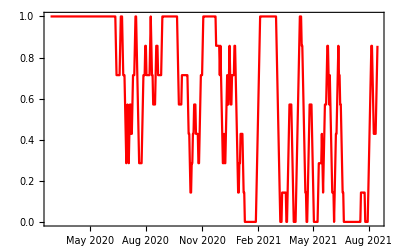
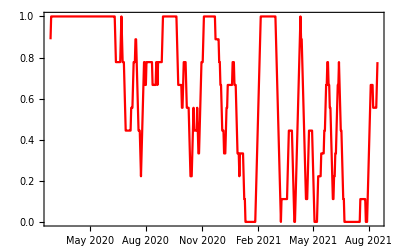

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

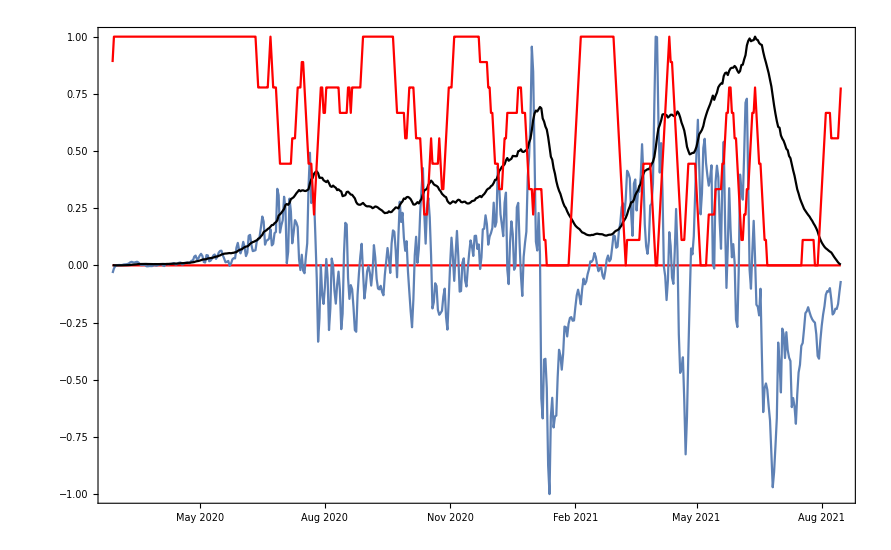

```mathematica
Show[DateListPlot[Transpose[{d$#ate,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%[[-1]]]
```

```mathematica
Table[Count[Round[#],Alternatives[Sequence@@Range[-300,300]]]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

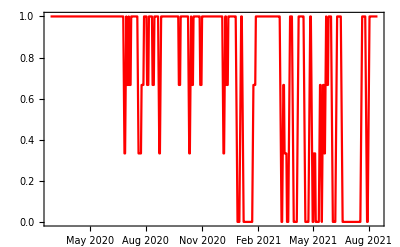
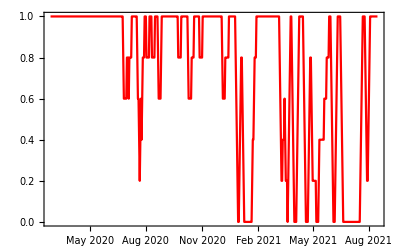
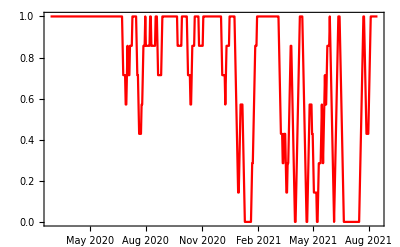
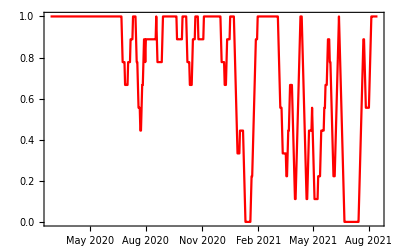

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

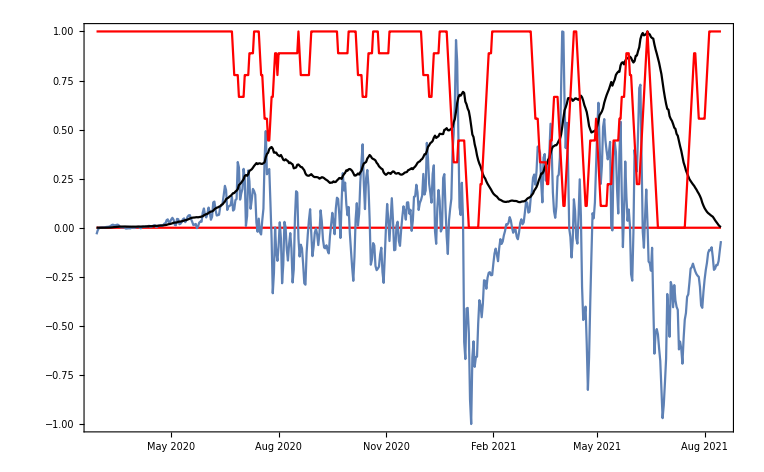

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%[[-1]]](*a medida que se aumenta el umbral se pierde resolusion*)
```

```mathematica
(***************Sacando las fechas del "mejor" resultado)
```

```mathematica
fechasMejor=Transpose[{DateObject[#,"Month"]&/@date,date,mejor[[-1]]}];
```

```mathematica
fechasValleys=Select[fechasMejor,#[[3]]==Max[fechasMejor[[All,-1]]]&]//GroupBy[#,First]&
```

<|Feb 2020→{{Feb 2020,Sat 29 Feb 2020,9}},Mar 2020→{{Mar 2020,Sun 1 Mar 2020,9},{Mar 2020,Mon 2 Mar 2020,9},{Mar 2020,Tue 3 Mar 2020,9},{Mar 2020,Wed 4 Mar 2020,9},{Mar 2020,Thu 5 Mar 2020,9},{Mar 2020,Fri 6 Mar 2020,9},{Mar 2020,Sat 7 Mar 2020,9},{Mar 2020,Sun 8 Mar 2020,9},{Mar 2020,Mon 9 Mar 2020,9},{Mar 2020,Tue 10 Mar 2020,9},{Mar 2020,Wed 11 Mar 2020,9},{Mar 2020,Thu 12 Mar 2020,9},{Mar 2020,Fri 13 Mar 2020,9},{Mar 2020,Sat 14 Mar 2020,9},{Mar 2020,Sun 15 Mar 2020,9},{Mar 2020,Mon 16 Mar 2020,9},{Mar 2020,Tue 17 Mar 2020,9},{Mar 2020,Wed 18 Mar 2020,9},{Mar 2020,Thu 19 Mar 2020,9},{Mar 2020,Fri 20 Mar 2020,9},{Mar 2020,Sat 21 Mar 2020,9},{Mar 2020,Sun 22 Mar 2020,9},{Mar 2020,Mon 23 Mar 2020,9},{Mar 2020,Tue 24 Mar 2020,9},{Mar 2020,Wed 25 Mar 2020,9},{Mar 2020,Thu 26 Mar 2020,9},{Mar 2020,Fri 27 Mar 2020,9},{Mar 2020,Sat 28 Mar 2020,9},{Mar 2020,Sun 29 Mar 2020,9},{Mar 2020,Mon 30 Mar 2020,9},{Mar 2020,Tue 31 Mar 2020,9}},Apr 2020→{{Apr 2020,Wed 1 Apr 2020,9},{Apr 2020,Thu 2 Apr 2020,9},{Apr 2020,Fri 3 Apr 2020,9},{Apr 2020,Sat 4 Apr 2020,9},{Apr 2020,Sun 5 Apr 2020,9},{Apr 2020,Mon 6 Apr 2020,9},{Apr 2020,Tue 7 Apr 2020,9},{Apr 2020,Wed 8 Apr 2020,9},{Apr 2020,Thu 9 Apr 2020,9},{Apr 2020,Fri 10 Apr 2020,9},{Apr 2020,Sat 11 Apr 2020,9},{Apr 2020,Sun 12 Apr 2020,9},{Apr 2020,Mon 13 Apr 2020,9},{Apr 2020,Tue 14 Apr 2020,9},{Apr 2020,Wed 15 Apr 2020,9},{Apr 2020,Thu 16 Apr 2020,9},{Apr 2020,Fri 17 Apr 2020,9},{Apr 2020,Sat 18 Apr 2020,9},{Apr 2020,Sun 19 Apr 2020,9},{Apr 2020,Mon 20 Apr 2020,9},{Apr 2020,Tue 21 Apr 2020,9},{Apr 2020,Wed 22 Apr 2020,9},{Apr 2020,Thu 23 Apr 2020,9},{Apr 2020,Fri 24 Apr 2020,9},{Apr 2020,Sat 25 Apr 2020,9},{Apr 2020,Sun 26 Apr 2020,9},{Apr 2020,Mon 27 Apr 2020,9},{Apr 2020,Tue 28 Apr 2020,9},{Apr 2020,Wed 29 Apr 2020,9},{Apr 2020,Thu 30 Apr 2020,9}},May 2020→{{May 2020,Fri 1 May 2020,9},{May 2020,Sat 2 May 2020,9},{May 2020,Sun 3 May 2020,9},{May 2020,Mon 4 May 2020,9},{May 2020,Tue 5 May 2020,9},{May 2020,Wed 6 May 2020,9},{May 2020,Thu 7 May 2020,9},{May 2020,Fri 8 May 2020,9},{May 2020,Sat 9 May 2020,9},{May 2020,Sun 10 May 2020,9},{May 2020,Mon 11 May 2020,9},{May 2020,Tue 12 May 2020,9},{May 2020,Wed 13 May 2020,9},{May 2020,Thu 14 May 2020,9},{May 2020,Fri 15 May 2020,9},{May 2020,Sat 16 May 2020,9},{May 2020,Sun 17 May 2020,9},{May 2020,Mon 18 May 2020,9},{May 2020,Tue 19 May 2020,9},{May 2020,Wed 20 May 2020,9},{May 2020,Thu 21 May 2020,9},{May 2020,Fri 22 May 2020,9},{May 2020,Sat 23 May 2020,9},{May 2020,Sun 24 May 2020,9},{May 2020,Mon 25 May 2020,9},{May 2020,Tue 26 May 2020,9},{May 2020,Wed 27 May 2020,9},{May 2020,Thu 28 May 2020,9},{May 2020,Fri 29 May 2020,9},{May 2020,Sat 30 May 2020,9},{May 2020,Sun 31 May 2020,9}},Jun 2020→{{Jun 2020,Mon 1 Jun 2020,9},{Jun 2020,Tue 2 Jun 2020,9},{Jun 2020,Wed 3 Jun 2020,9},{Jun 2020,Thu 4 Jun 2020,9},{Jun 2020,Fri 5 Jun 2020,9},{Jun 2020,Sat 6 Jun 2020,9},{Jun 2020,Sun 7 Jun 2020,9},{Jun 2020,Mon 8 Jun 2020,9},{Jun 2020,Tue 9 Jun 2020,9},{Jun 2020,Wed 10 Jun 2020,9}},Sep 2020→{{Sep 2020,Fri 4 Sep 2020,9},{Sep 2020,Sat 5 Sep 2020,9},{Sep 2020,Sun 6 Sep 2020,9},{Sep 2020,Mon 7 Sep 2020,9},{Sep 2020,Tue 8 Sep 2020,9},{Sep 2020,Wed 9 Sep 2020,9},{Sep 2020,Thu 10 Sep 2020,9},{Sep 2020,Fri 11 Sep 2020,9},{Sep 2020,Sat 12 Sep 2020,9},{Sep 2020,Sun 13 Sep 2020,9},{Sep 2020,Mon 14 Sep 2020,9},{Sep 2020,Tue 15 Sep 2020,9}},Nov 2020→{{Nov 2020,Wed 11 Nov 2020,9},{Nov 2020,Thu 12 Nov 2020,9},{Nov 2020,Fri 13 Nov 2020,9},{Nov 2020,Sat 14 Nov 2020,9},{Nov 2020,Sun 15 Nov 2020,9},{Nov 2020,Mon 16 Nov 2020,9},{Nov 2020,Tue 17 Nov 2020,9},{Nov 2020,Wed 18 Nov 2020,9},{Nov 2020,Thu 19 Nov 2020,9},{Nov 2020,Fri 20 Nov 2020,9}},Feb 2021→{{Feb 2021,Wed 10 Feb 2021,9},{Feb 2021,Thu 11 Feb 2021,9},{Feb 2021,Fri 12 Feb 2021,9},{Feb 2021,Sat 13 Feb 2021,9},{Feb 2021,Sun 14 Feb 2021,9},{Feb 2021,Mon 15 Feb 2021,9},{Feb 2021,Tue 16 Feb 2021,9},{Feb 2021,Wed 17 Feb 2021,9},{Feb 2021,Thu 18 Feb 2021,9},{Feb 2021,Fri 19 Feb 2021,9},{Feb 2021,Sat 20 Feb 2021,9},{Feb 2021,Sun 21 Feb 2021,9},{Feb 2021,Mon 22 Feb 2021,9},{Feb 2021,Tue 23 Feb 2021,9},{Feb 2021,Wed 24 Feb 2021,9},{Feb 2021,Thu 25 Feb 2021,9},{Feb 2021,Fri 26 Feb 2021,9},{Feb 2021,Sat 27 Feb 2021,9},{Feb 2021,Sun 28 Feb 2021,9}}|>

```mathematica
(*NOTA_ El primer valle es muy largo, he incluye los meses de febrero a  junio. Los ultimos tres meses son los ultimos valle. Pero este identifica como unica ola los ultimos dos picos porque entre estos no hay un valle largo*)
```

```mathematica
dateStartWave={DateObject[{2020,5,1},"Day","Gregorian",-5.](*I selected manually this as the initial date of the first wave*),Sequence@@(#[[Round[Length[#]/2],2]]&/@Values[fechasValleys[[-3;;]]])(*those are the start date of the 2-4 waves*),DateObject[{2021,05,01}](*I selected manually this as the initial date of the 5 wave*),date[[-1]](*the end*)}
```

```mathematica
dateStartWave={DateObject[{2020,5,1},"Day","Gregorian",-5.],DateObject[{2020,9,9},"Day","Gregorian",-5.],DateObject[{2020,11,15},"Day","Gregorian",-5.],DateObject[{2021,2,19},"Day","Gregorian",-5.],DateObject[{2021,5,1},"Day","Gregorian",-5.],DateObject[{2021,8,15},"Day","Gregorian",-5.]}
```

{Fri 1 May 2020,Wed 9 Sep 2020,Sun 15 Nov 2020,Fri 19 Feb 2021,Sat 1 May 2021,Sun 15 Aug 2021}

```mathematica
p1=DateListPlot[Transpose[{date,normalDerivada}],PlotStyle->Opacity[0.6,RGBColor[0.1,0.6,0.8]]];
```

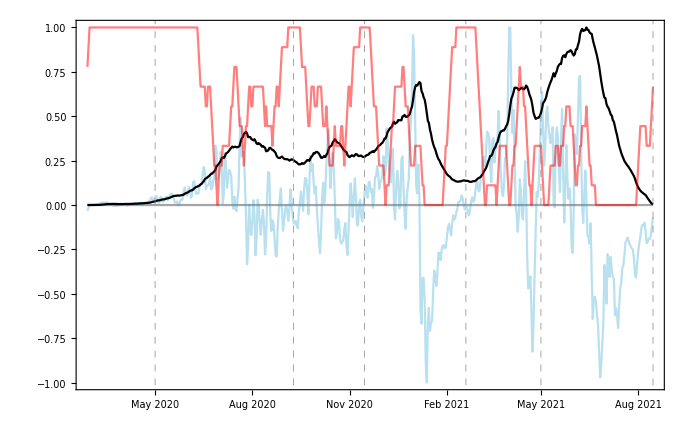

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Opacity[0.7,Gray],GridLines->{dateStartWave[[All,1]],None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,20]],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],DateListPlot[Transpose[{date,mejor[[-1]]/Max[mejor[[-1]]]}],PlotStyle->Opacity[0.5,Red]]]
```

```mathematica
p1=DateListPlot[Transpose[{date,normalDerivada}],PlotStyle->Opacity[0.3,RGBColor[0.1,0.6,0.8]]];
```

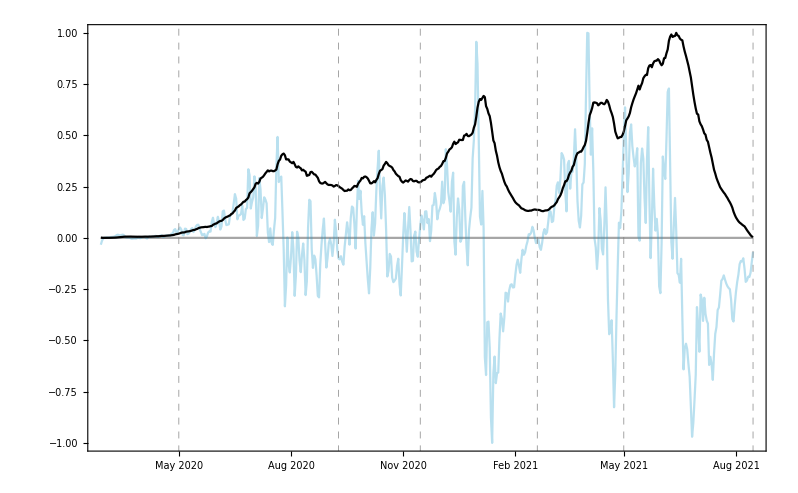

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Opacity[0.7,Gray],GridLines->{dateStartWave[[All,1]],None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,20]],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black]]
```

```mathematica
dateStartWave
```

{Fri 1 May 2020,Wed 9 Sep 2020,Sun 15 Nov 2020,Fri 19 Feb 2021,Sat 1 May 2021,Sun 15 Aug 2021}

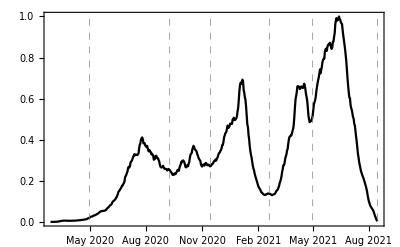

```mathematica
DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black,GridLines->{dateStartWave[[All,1]],None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,11],DateTicksFormat->{"Year","/","MonthShort"},FrameTicks->{{Automatic,Automatic},{{{2020,5,1},{2020,9,9},{2020,11,15},{2021,2,19},{2021,5,1},{2021,8,15}},Automatic}}]
```

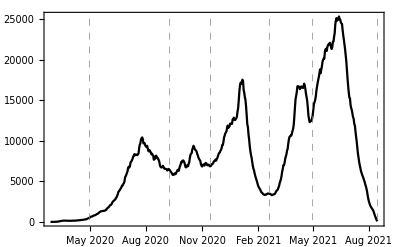

```mathematica
DateListPlot[Transpose[{date,smoothCases}],PlotStyle->Black,GridLines->{dateStartWave[[All,1]],None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,15]]
```

```mathematica
(*dates star-final valley and peak*)
```

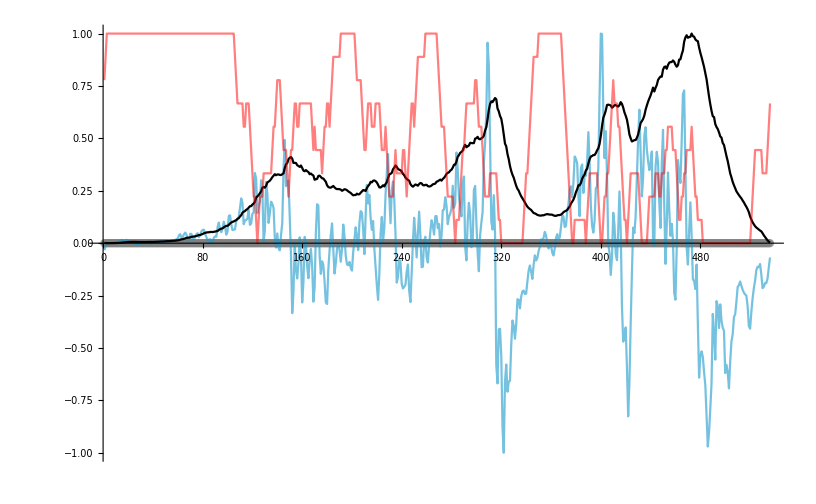

```mathematica
Show[ListPlot[Table[0,Length[case]],PlotStyle->Opacity[0.7,Gray]],ListPlot[normalDerivada,PlotStyle->Opacity[0.6,RGBColor[0.1,0.6,0.8]],Joined->True],ListPlot[smoothCases/Max[smoothCases],PlotStyle->Black,Joined->True],ListPlot[mejor[[-1]]/Max[mejor[[-1]]],PlotStyle->Opacity[0.5,Red],Joined->True]]
```

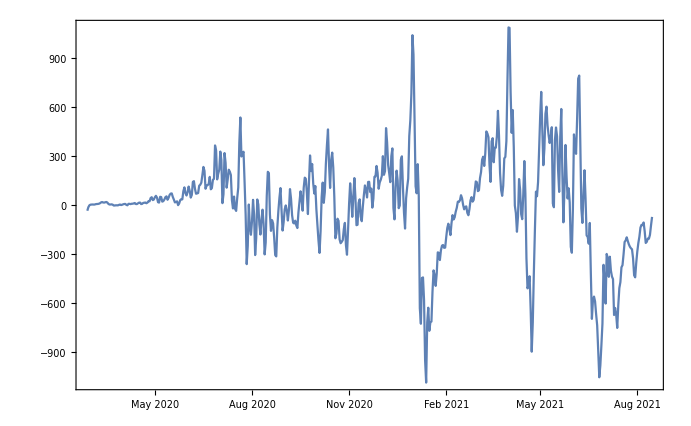

```mathematica
DateListPlot[Transpose[{date,firstDerivate}]]
```

```mathematica
Table[Count[Round[#],(x_/;x<-100)|(x_/;x>100)]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

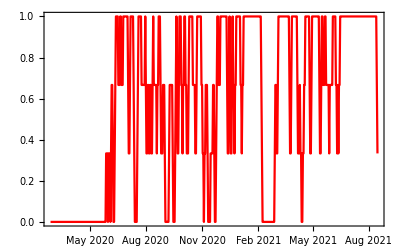
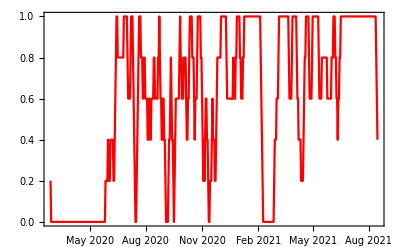
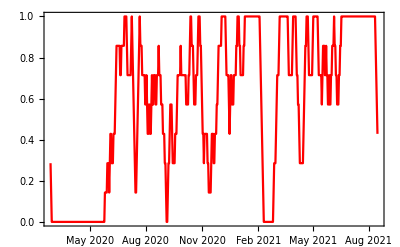
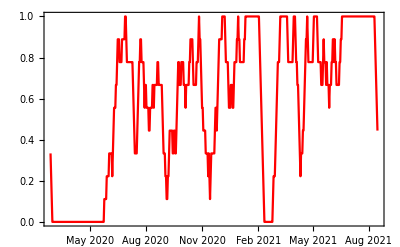

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

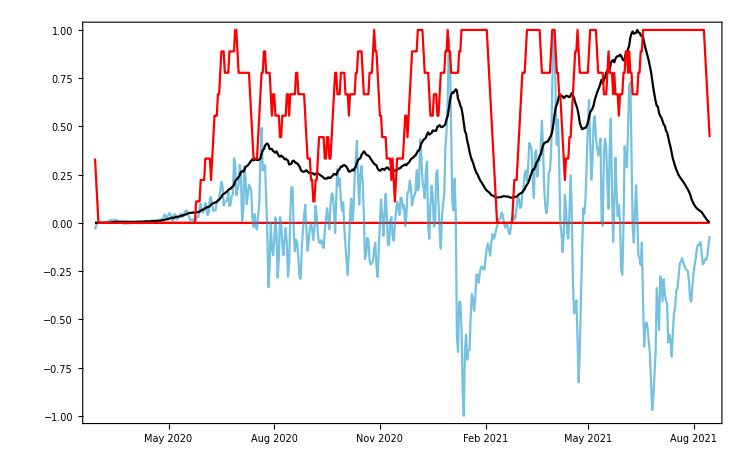

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%[[-1]]]
```

```mathematica
mejor2=Table[Count[Round[#],(x_/;x<-200)|(x_/;x>200)]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

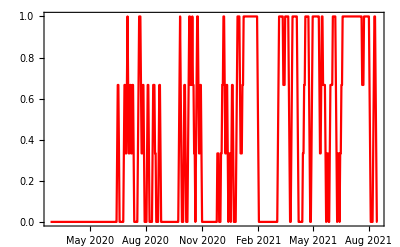
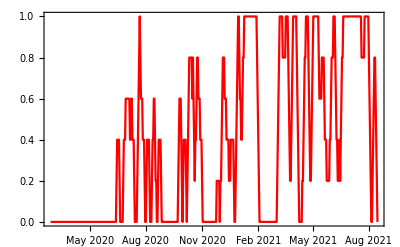
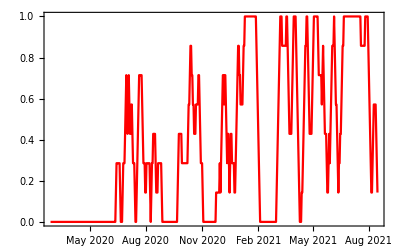
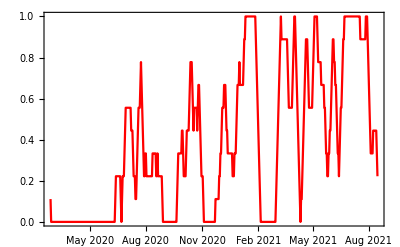

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

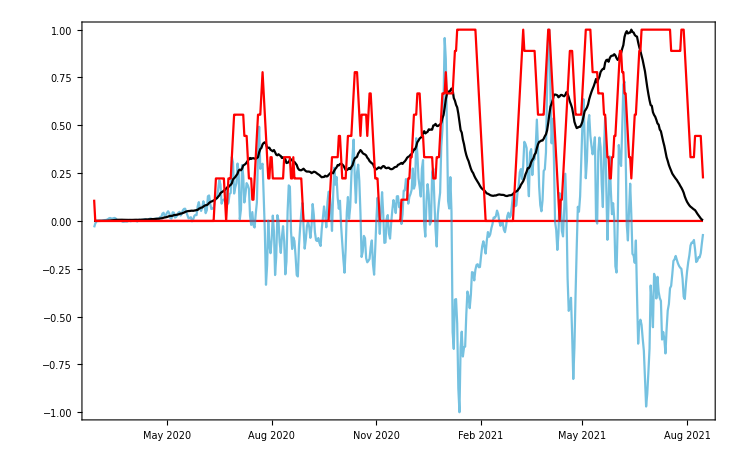

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%[[-1]]]
```

```mathematica
Table[Count[Round[#],(x_/;x<-250)|(x_/;x>250)]&/@Transpose[{Sequence@@(NestList[RotateLeft[#]&,firstDerivate,i][[2;;]]),firstDerivate,Sequence@@(NestList[RotateRight[#]&,firstDerivate,i][[2;;]])}],{i,{1,2,3,4}}];
```

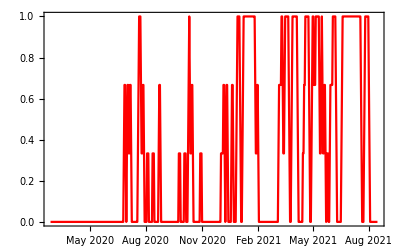
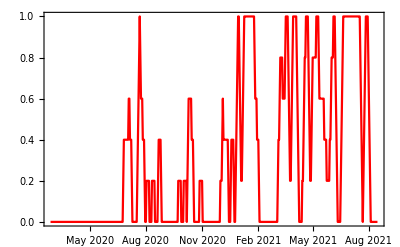
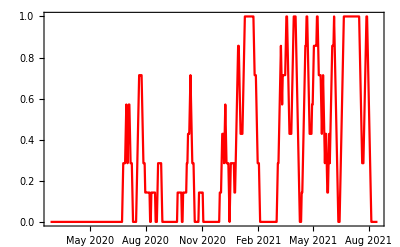
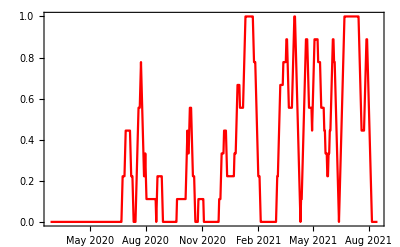

```mathematica
DateListPlot[Transpose[{date,#/Max[#]}],PlotStyle->Red]&/@%
```

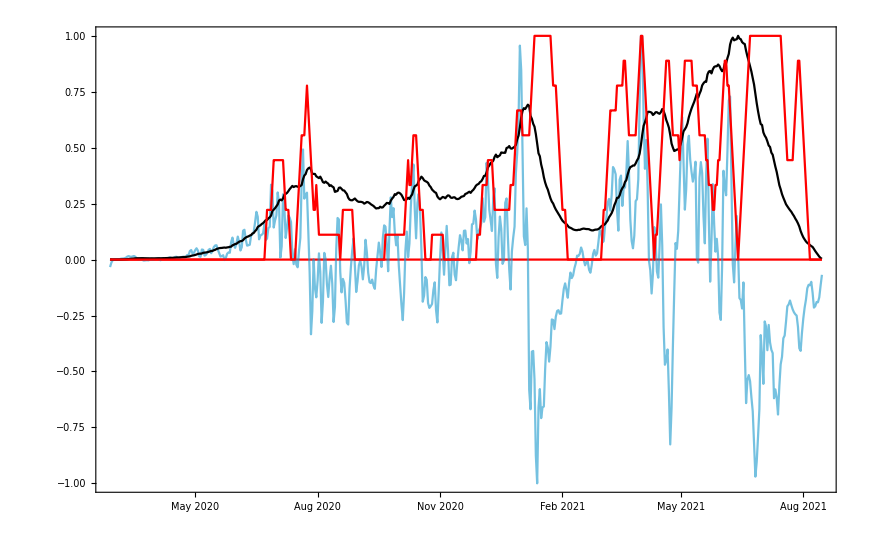

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Red],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],%[[-1]]](*a medida que se aumenta el umbral se pierde resolusion*)
```

```mathematica
(*Iam selecting manually the dates using the "mejor" previous plots*)
```

```mathematica
ListPlot[#/Max[#],PlotStyle->Red,Joined->True]&/@{%[[-1]]}
```

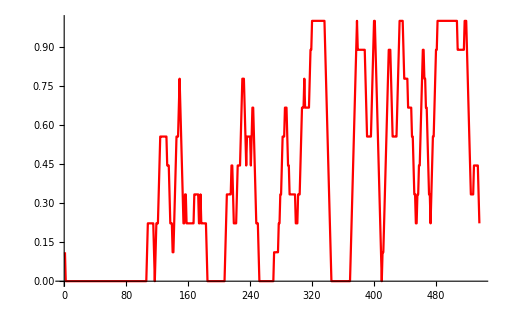
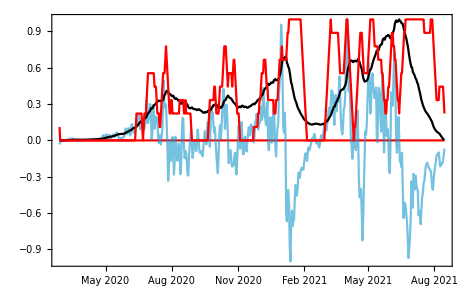

```mathematica
dateValleysPeaks=date[[{1,127,170,215,244,283,330,382,423,434,504,-1}]]
```

```mathematica
dateValleysPeaks={DateObject[{2020,2,27},"Day","Gregorian",-5.],DateObject[{2020,7,2},"Day","Gregorian",-5.],DateObject[{2020,8,14},"Day","Gregorian",-5.],DateObject[{2020,9,28},"Day","Gregorian",-5.],DateObject[{2020,10,27},"Day","Gregorian",-5.],DateObject[{2020,12,5},"Day","Gregorian",-5.],DateObject[{2021,1,21},"Day","Gregorian",-5.],DateObject[{2021,3,14},"Day","Gregorian",-5.],DateObject[{2021,4,24},"Day","Gregorian",-5.],DateObject[{2021,5,5},"Day","Gregorian",-5.],DateObject[{2021,7,14},"Day","Gregorian",-5.],DateObject[{2021,8,15},"Day","Gregorian",-5.]}
```

{Thu 27 Feb 2020,Thu 2 Jul 2020,Fri 14 Aug 2020,Mon 28 Sep 2020,Tue 27 Oct 2020,Sat 5 Dec 2020,Thu 21 Jan 2021,Sun 14 Mar 2021,Sat 24 Apr 2021,Wed 5 May 2021,Wed 14 Jul 2021,Sun 15 Aug 2021}

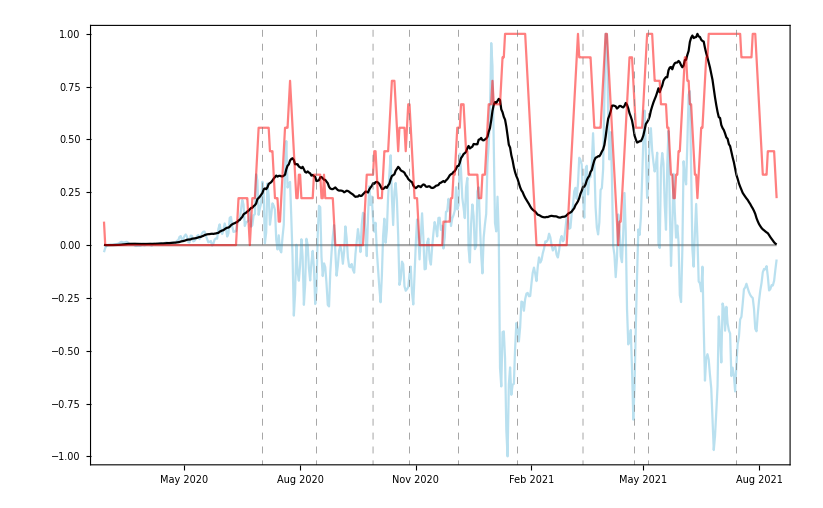

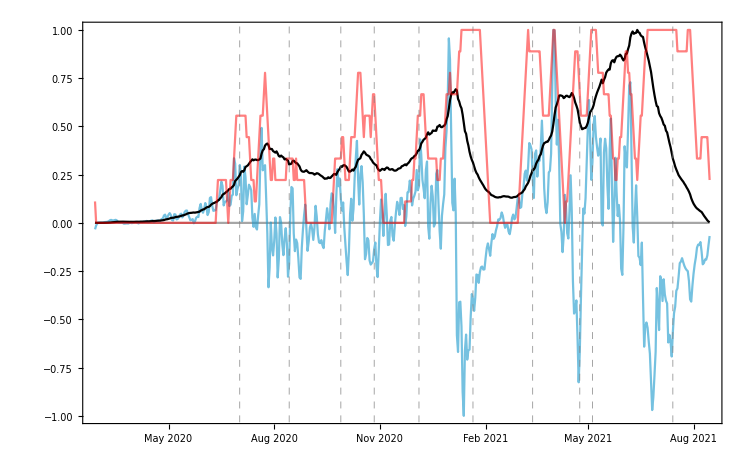

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Opacity[0.7,Gray],GridLines->{dateValleysPeaks,None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,20]],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black],DateListPlot[Transpose[{date,mejor2[[-1]]/Max[mejor2[[-1]]]}],PlotStyle->Opacity[0.5,Red]]]
```

```mathematica
p1=DateListPlot[Transpose[{date,normalDerivada}],PlotStyle->Opacity[0.3,RGBColor[0.1,0.6,0.8]]];
```

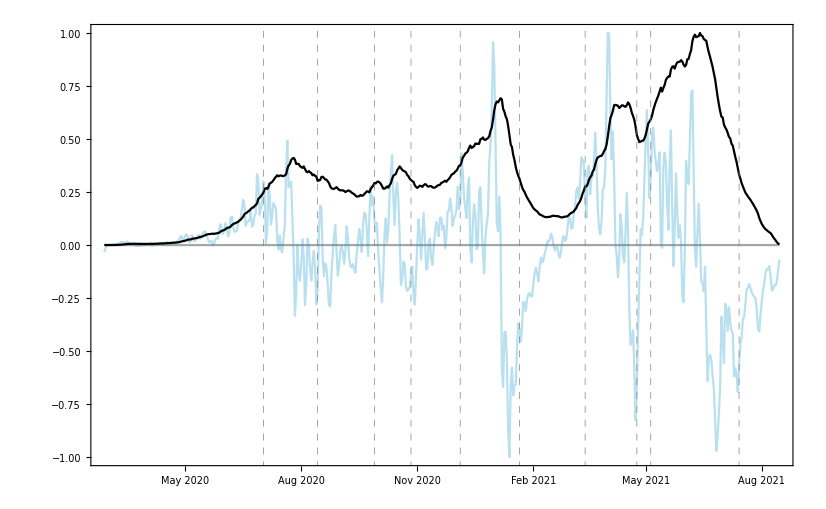

{Thu 27 Feb 2020,Thu 2 Jul 2020,Fri 14 Aug 2020,Mon 28 Sep 2020,Tue 27 Oct 2020,Sat 5 Dec 2020,Thu 21 Jan 2021,Sun 14 Mar 2021,Sat 24 Apr 2021,Wed 5 May 2021,Wed 14 Jul 2021,Sun 15 Aug 2021}

```mathematica
Show[DateListPlot[Transpose[{date,Table[0,Length[case]]}],PlotStyle->Opacity[0.7,Gray],GridLines->{dateValleysPeaks,None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,20]],p1,DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black]]
```

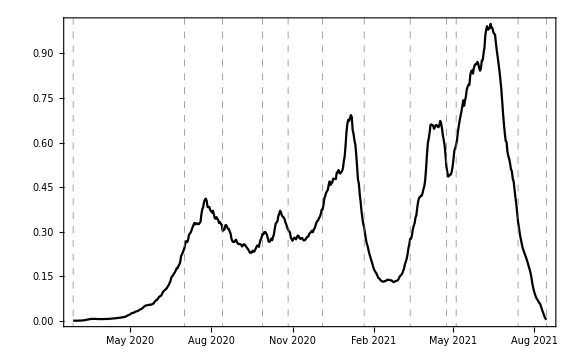

```mathematica
DateListPlot[Transpose[{date,smoothCases/Max[smoothCases]}],PlotStyle->Black,GridLines->{dateValleysPeaks,None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,12],DateTicksFormat->{"Year","/","MonthShort"},FrameTicks->{{Automatic,Automatic},{{{2020,2,27},{2020,7,2},{2021,9,28},{2020,12,5},{2021,4,24},{2021,8,15}},Automatic}}]
```

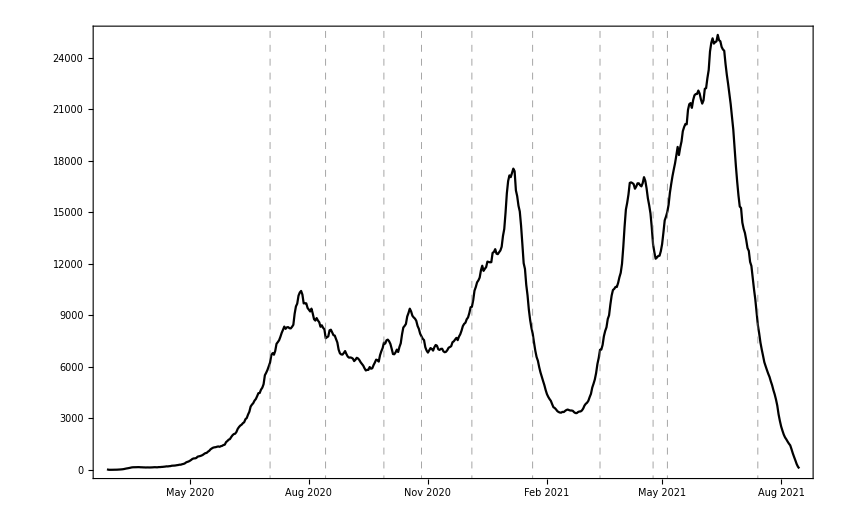

```mathematica
DateListPlot[Transpose[{date,smoothCases}],PlotStyle->Black,GridLines->{dateValleysPeaks,None},GridLinesStyle->Directive[Gray,Dashed,Thick],FrameTicksStyle->Directive[Black,15]]
```

database with this co variables

```mathematica
dateStartWave[[All,1]]
```

```mathematica
dateValleysPeaks
```

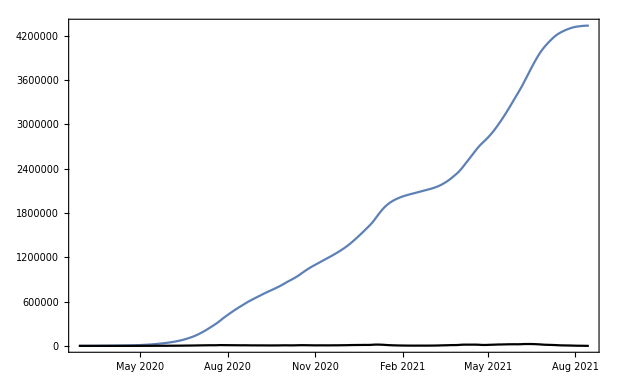

```mathematica
Show[{-Graphics-,-Graphics-}]
```